```mathematica
Quit
```

```mathematica
Needs["CCompilerDriver`"];
compileDir=FileNameJoin[{"~/Documents/wolfram/git/nks17/nikhil/project/build"}]
```

~/Documents/wolfram/git/nks17/nikhil/project/build

```mathematica
If[ValueQ[lib]&&StringQ[lib]&&FileExistsQ[lib],DeleteFile[lib]];
lib=CreateLibrary[
{"/Users/ijohnson/Documents/wolfram/git/nks17/nikhil/project/CSource/libtinslink.cpp"},
"libtinslink",
"IncludeDirectories"->{"/usr/local/Cellar/libtins/3.5/include/"},
"Libraries"->{"tins","stdc++"},
"Language"->"C++",
"CompilerName"->"clang",
"CompileOptions"->{"-std=c++11","-g","-O0","-Wall","-pedantic"},
"ShellCommandFunction"->Print,
"TargetDirectory"->compileDir,
"CleanIntermediate"->False
]
```

/usr/bin/clang -dynamiclib -o "/Users/ijohnson/Documents/wolfram/git/nks17/nikhil/project/build/Working-ijohnson2maclap-73549-2127462400-1/libtinslink.dylib" -m64 -x c++ -fPIC -O2 -mmacosx-version-min=10.9 -framework Foundation -std=c++11 -g -O0 -Wall -pedantic  -I"/Applications/Mathematica 11.1.1.app/Contents/SystemFiles/IncludeFiles/C" -I"/Applications/Mathematica 11.1.1.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions" -I"/usr/local/Cellar/libtins/3.5/include" "/Users/ijohnson/Documents/wolfram/git/nks17/nikhil/project/CSource/libtinslink.cpp"  -F"/Applications/Mathematica 11.1.1.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions"  -framework "mathlink" -l"tins" -l"stdc++" -lc++ 2>&1

/Users/ijohnson/Documents/wolfram/git/nks17/nikhil/project/build/libtinslink.dylib

/usr/bin/clang -dynamiclib -o "/Users/ijohnson/Documents/wolfram/git/nks17/nikhil/project/build/Working-ijohnson2maclap-69621-2127462400-16/libtinslink.dylib" -m64 -x c++ -fPIC -O2 -mmacosx-version-min=10.9 -framework Foundation -std=c++11 -g -O0 -Wall -pedantic  -I"/Applications/Mathematica 11.1.1.app/Contents/SystemFiles/IncludeFiles/C" -I"/Applications/Mathematica 11.1.1.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions" -I"/usr/local/Cellar/libtins/3.5/include" "/Users/ijohnson/Documents/wolfram/git/nks17/nikhil/project/CSource/libtinslink.cpp"  -F"/Applications/Mathematica 11.1.1.app/Contents/SystemFiles/Links/MathLink/DeveloperKit/MacOSX-x86-64/CompilerAdditions"  -framework "mathlink" -l"tins" -l"stdc++" -lc++ 2>&1

```mathematica
lib="/Users/ijohnson/Documents/wolfram/git/nks17/nikhil/project/build/libtinslink.dylib";
```

```mathematica
LibraryUnload["/Users/ijohnson/Documents/wolfram/git/nks17/nikhil/project/build/libtinslink.dylib"]
```

```mathematica
LibraryLoad[lib]
```

```mathematica
StartFunction=LibraryFunctionLoad[lib,"StartTCPSniffing",{String},"Void"]
```

LibraryFunction[…]

```mathematica
StopFunction=LibraryFunctionLoad[lib,"StopTCPSniffing",{},"Void"]
```

LibraryFunction[…]

```mathematica
emptyPackets=LibraryFunctionLoad[lib,"EmptyTCPSniffingHashTable",{},{Integer,1}]
```

LibraryFunction[…]

```mathematica
(StartFunction["en0"];
Pause[30];
StopFunction[];
data=emptyPackets[];
rest=data;
Dataset@First@Last@Reap[While[rest=!={},
(
{{len},rest}=TakeDrop[rest,1];
{packet,rest}=TakeDrop[rest,len];
{{strLen},payload}=TakeDrop[packet,1];
{str,payload}=TakeDrop[payload,strLen];
k=FromCharacterCode[str];
y1=AssociationThread[{"SourceIP","SourcePort","DestinationIP","DestinationPort","SequenceNumber","AcknowledgementSequenceNumber","Window","Checksum","Urgent Pointer","Data Offset","Flags","Header Size","TimeSeconds","TimeMicroseconds"},StringTrim/@StringSplit[k,{":","to","seq","ack_seq","window","checksum","urgentpointer","dataoffset","flags","headersize","ts","tus"}]];
y1=Append[KeyDrop[{"TimeSeconds","TimeMicroseconds"}]@y1,"Timestamp"->FromUnixTime@FromDigits@y1["TimeSeconds"]+Quantity[FromDigits[y1["TimeMicroseconds"]],"Microseconds"]];
Sow[Append[MapAt[ToCharacterCode[#,"UTF8"]&,Key["Data Offset"]]@y1,"Payload"->ByteArray[payload]]]
)
]
])
```

Dataset[<>]

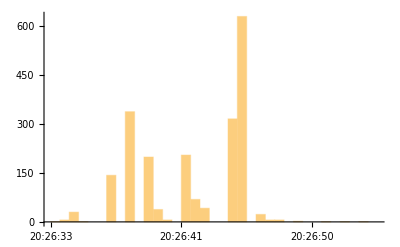

```mathematica
DateHistogram[Normal[First[GroupBy[%9,"DestinationIP"]][All,"Timestamp"]]]
```

```mathematica
ByteArray[{1,2,3}]//Length
```

3

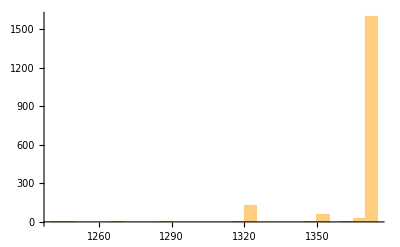

```mathematica
Histogram[Length/@Normal[First[GroupBy[%9,"DestinationIP"]][All,"Payload"]]]
```

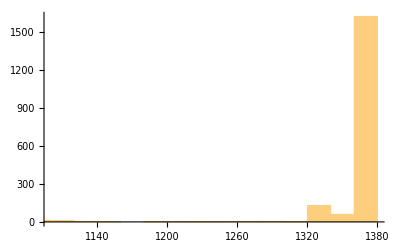

```mathematica
Histogram[Length/@Normal[%9[All,"Payload"]]]
```

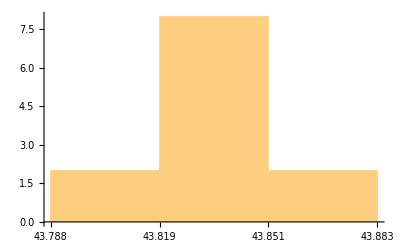

```mathematica
DateHistogram[Last[GroupBy[%11,"DestinationIP"]][All,"Timestamp"]]
```

```mathematica
%11[All,{"TimeSeconds"->FromUnixTime@*FromDigits,"TimeMicroseconds"->(Quantity[FromDigits[#],"Microseconds"]&)}]
```

Dataset[<>]

```mathematica
%13[All,(Append[KeyDrop[{"TimeSeconds","TimeMicroseconds"}]@#,"Timestamp"->#["TimeSeconds"]+#["TimeMicroseconds"]]&)]
```

KeyDrop::invrl: The argument TimeSeconds is not a valid Association or a list of rules.

Dataset[<>]

```mathematica
FromCharacterCode@*Normal/@Normal@Select[%22,#["SourcePort"]=="80"&][All,"Payload"]
```

{HTTP/1.1 301 Moved Permanently\r
Location: http://www.google.com/\r
Content-Type: text/html; charset=UTF-8\r
Date: Tue, 04 Jul 2017 23:26:40 GMT\r
Expires: Thu, 03 Aug 2017 23:26:40 GMT\r
Cache-Control: public, max-age=2592000\r
Server: gws\r
Content-Length: 219\r
X-XSS-Protection: 1; mode=block\r
X-Frame-Options: SAMEORIGIN\r
\r
<HTML><HEAD><meta http-equiv="content-type" content="text/html;charset=utf-8">
<TITLE>301 Moved</TITLE></HEAD><BODY>
<H1>301 Moved</H1>
The document has moved
<A HREF="http://www.google.com/">here</A>.\r
</BODY></HTML>\r
}

```mathematica
FromCharacterCode@*Normal/@Normal[%22[All,"Payload"]]
```

{.17.03.03.00üuÑ.17.15.bcå©ã.95¶j6.04.8d .93\5æýOÑ.87_úøÂ.bd.9d.91¤ÇæÂzyDAà.aa.12¶.87.10ZÛ .9dB.8f[.81bWÜ.04ÔP.92>Â×.90.03h+ä?sõç	ÅØ\rÚq.bab.7f.13üÅÿÜ.14Y.12ÇÏ"Bj.1aÁ1=ÔàÚÛu.12ÿ¬.87.0bµ.b9.0f.84>.82i.8d.18ú\f.bd,.8déï]Úai.baÇt6÷O#ã%Îæ	]¢\].1deaÞÇ.11.90§.bdmWN.04ÔRæ.83Hæ.94.9d,t.01ü.8d.1a¿&.9b>ñ|I.9a.9a.b2{ÚÈ¶u.01.152óñµf.9e]¨âùXç
.0e)<.06âõCwA6Ó.90Ùm¿|.9ae!.80MA.95ëÀ.193.af;.00»U@#
ÇÆ!kí».0e.0eÂaò)b.1a=Û,.17.03.03.03øPÔ.84.99ì*.02wû\f.03}.9d9/.86.85.10OfSq.a6Ì°EÕ.99Æ¸.08l.92
.90&.baP!.95ô|$.9f]"Ò.8f.03.82TCx.8aKzÙY.8cö2.8bJ8.134?ò.81MñoµÌ.b948.9ax;Ä.19.bdFa,.19.86.85.075Ýe.91.04Ñ.9fMD.96<úù_.1f.12¸YÃ LY.b9Ì(ÒôF»â.04.04C.1eòem2ç.9f.9fx~9.0e¤E<êf<J.80.87«.8b|.7f.96¨ã^c.b4DY.18.9dVÌèch.b9ÍX.06tu.16O.aaÁ.9d.11Ât×ÞÆ.01Ðie.ba.08B.9aUn<.b9.91=Uà.83Toqó"gïüõ·Ï`6.1c.95ìÕD.1c.b4ûYÒf.00R.17[.b2.91.b9V.98`B.1d.91.1f_ù.afý.8f.04<æþ£Ò.be.80@©Ë.b2.860¿p%.85.82R.9b.07.01.01Í'.88r.01æ»
.01h.9f.1c.95à.81§ïÇW.8f.8bQ.0f¬.7fò^.144l.82*.0b\fNlÄ:.8aI\f.13hmýÙ.94.1cî	.0e.12jcÚýúéV.88.1e.0b.06.123N2.08\Þ.81.bawýÿÍDgat¶f5Á.8bÓ.17V6.97-ß'.8fÐ.14.8e.97x)6ö.9b0.00,y!{Èrl.18+$.84øc.16uRío@V.98ï.1f.7fR.9dè.9f.19à\f.85.8d.08ñxIå	tIö+Tb°ì»K.81.8e[Y.8dý}R.93ÁòðÙtR.13.b2yl.96µaø%,ô.00ïR\rÈx\d!.1e¡.95#Q$3q.1fÓ.00Sí0Y.88.95õ~.19Ñ3.bc.95~.92ãTüW.1f(.159ÿîw]t.85*D.81~ÒT`VÔÚVÑ.11.©à>w.85.1fY¨Ë`s .b3P/.86Á.17ßõ~p7
t.8aÑ.95é.8f.97jGe.08{*¢ìhx.90.89.aa1.1f(+.1e.be.93Ã.1fiÿU.b2DÙ\rs.97.9e*¤ÿ.8d«wúáG·ö.84çâã©.93Ä.9d.16.97l.95`.7fô£2Ür{.991]I.92.b3.03ð.8f.b4.1dæF8.80Û.be©.12.8aYß¬{b.13ÒØ÷.00FÌÑPó©«].05.89Ûa.04D.1fàÆð°óYÒé.18À.9eC.89.9b.b4à.9eÌ.06	ø¥4þ.8fjB`.1e.b9|SHå.bc.89.1d¢.99.163Ð.0b°.9d.92.90Þ.86O.91.9f
ì.94.98.99.b9Í&J.b95õU.17 $Ö.b2.a6ÛÒ[i[6Y.baÿû.1aýZ<
FëM.95.8bÿb.07ÓM4|·[à
p/\fs5.82.h.18.1f.1e.1e{ôÚoï§áf.0fûTæràÞ£bö	.1cÐµ.96^lSÐP.02ÎMF.08.92Y4\Ö)\fÕ.01a·.9cÏÞdÉG.87{ó2e\f,J.00L.02ÛÕ®.14.19ü·1ã{5xÑ.1d.9a Y.1cñæ)µÏÛå.bcSÕ.02ü¿kRl.10£.16.1fË$á¥.18.14.1cÖ9ý/Sr.8aG3.84.88.04ceÝ\r.11.06.90U@À.85t.8déÊÀ.0b¬.1e£òÁ¶ðöÁáÀXÞIU.07ÝNö°.be.8b.93.9f.1d8.18è.05±o5ä.8dñÝeÑ.88Ùùê.95Ý-¥a.81Í.15>.9ck.98h/6|¥Ie.b3.04ýX"\Â.0e^.943.16.84.02Õ.92.14£.84VÚ.b2.b3.13@i[Å.baÇ.8f<.8c«z	«÷.b9à£¢ÃA.825*óDÞ.91,.17.03.03.03øPÔ.84.99ì*.02wû\f.03}.9d9/.86.85.10OfSq.a6Ì°EÕ.99Æ¸.08l.92
.90&.baP!.95ô|$.9f]"Ò.8f.03.82TCx.8aKzÙY.8cö2.8bJ8.134?ò.81MñoµÌ.b948.9ax;Ä.19.bdFa,.19.86.85.075Ýe.91.04Ñ.9fMD.96<úù_.1f.12¸YÃ LY.b9Ì(ÒôF»â.04.04C.1eòem2ç.9f.9fx~9.0e¤E<êf<J.80.87«.8b|.7f.96¨ã^c.b4DY.18.9dVÌèch.b9ÍX.06tu.16O.aaÁ.9d.11Ât×ÞÆ.01Ðie.ba.08B.9aUn<.b9.91=Uà.83Toqó"gïüõ·Ï`6.1c.95ìÕD.1c.b4ûYÒf.00R.17[.b2.91.b9V.98`B.1d.91.1f_ù.afý.8f.04<æþ£Ò.be.80@©Ë.b2.860¿p%.85.82R.9b.07.01.01Í'.88r.01æ»
.01h.9f.1c.95à.81§ïÇW.8f.8bQ.0f¬.7fò^.144l.82*.0b\fNlÄ:.8aI\f.13hmýÙ.94.1cî	.0e.12jcÚýúéV.88.1e.0b.06.123N2.08\Þ.81.bawýÿÍDgat¶f5Á.8bÓ.17V6.97-ß'.8fÐ.14.8e.97x)6ö.9b0.00,y!{Èrl.18+$.84øc.16uRío@V.98ï.1f.7fR.9dè.9f.19à\f.85.8d.08ñxIå	tIö+Tb°ì»K.81.8e[Y.8dý}R.93ÁòðÙtR.13.b2yl.96µaø%,ô.00ïR\rÈx\d!.1e¡.95#Q$3q.1fÓ.00Sí0Y.88.95õ~.19Ñ3.bc.95~.92ãTüW.1f(.159ÿîw]t.85*D.81~ÒT`VÔÚVÑ.11.©à>w.85.1fY¨Ë`s .b3P/.86Á.17ßõ~p7
t.8aÑ.95é.8f.97jGe.08{*¢ìhx.90.89.aa1.1f(+.1e.be.93Ã.1fiÿU.b2DÙ\rs.97.9e*¤ÿ.8d«wúáG·ö.84çâã©.93Ä.9d.16.97l.95`.7fô£2Ür{.991]I.92.b3.03ð.8f.b4.1dæF8.80Û.be©.12.8aYß¬{b.13ÒØ÷.00FÌÑPó©«].05.89Ûa.04D.1fàÆð°óYÒé.18À.9eC.89.9b.b4à.9eÌ.06	ø¥4þ.8fjB`.1e.b9|SHå.bc.89.1d¢.99.163Ð.0b°.9d.92.90Þ.86O.91.9f
ì.94.98.99.b9Í&J.b95õU.17 $Ö.b2.a6ÛÒ[i[6Y.baÿû.1aýZ<
FëM.95.8bÿb.07ÓM4|·[à
p/\fs5.82.h.18.1f.1e.1e{ôÚoï§áf.0fûTæràÞ£bö	.1cÐµ.96^lSÐP.02ÎMF.08.92Y4\Ö)\fÕ.01a·.9cÏÞdÉG.87{ó2e\f,J.00L.02ÛÕ®.14.19ü·1ã{5xÑ.1d.9a Y.1cñæ)µÏÛå.bcSÕ.02ü¿kRl.10£.16.1fË$á¥.18.14.1cÖ9ý/Sr.8aG3.84.88.04ceÝ\r.11.06.90U@À.85t.8déÊÀ.0b¬.1e£òÁ¶ðöÁáÀXÞIU.07ÝNö°.be.8b.93.9f.1d8.18è.05±o5ä.8dñÝeÑ.88Ùùê.95Ý-¥a.81Í.15>.9ck.98h/6|¥Ie.b3.04ýX"\Â.0e^.943.16.84.02Õ.92.14£.84VÚ.b2.b3.13@i[Å.baÇ.8f<.8c«z	«÷.b9à£¢ÃA.825*óDÞ.91,.17.03.03.03øPÔ.84.99ì*.02wû\f.03}.9d9/.86.85.10OfSq.a6Ì°EÕ.99Æ¸.08l.92
.90&.baP!.95ô|$.9f]"Ò.8f.03.82TCx.8aKzÙY.8cö2.8bJ8.134?ò.81MñoµÌ.b948.9ax;Ä.19.bdFa,.19.86.85.075Ýe.91.04Ñ.9fMD.96<úù_.1f.12¸YÃ LY.b9Ì(ÒôF»â.04.04C.1eòem2ç.9f.9fx~9.0e¤E<êf<J.80.87«.8b|.7f.96¨ã^c.b4DY.18.9dVÌèch.b9ÍX.06tu.16O.aaÁ.9d.11Ât×ÞÆ.01Ðie.ba.08B.9aUn<.b9.91=Uà.83Toqó"gïüõ·Ï`6.1c.95ìÕD.1c.b4ûYÒf.00R.17[.b2.91.b9V.98`B.1d.91.1f_ù.afý.8f.04<æþ£Ò.be.80@©Ë.b2.860¿p%.85.82R.9b.07.01.01Í'.88r.01æ»
.01h.9f.1c.95à.81§ïÇW.8f.8bQ.0f¬.7fò^.144l.82*.0b\fNlÄ:.8aI\f.13hmýÙ.94.1cî	.0e.12jcÚýúéV.88.1e.0b.06.123N2.08\Þ.81.bawýÿÍDgat¶f5Á.8bÓ.17V6.97-ß'.8fÐ.14.8e.97x)6ö.9b0.00,y!{Èrl.18+$.84øc.16uRío@V.98ï.1f.7fR.9dè.9f.19à\f.85.8d.08ñxIå	tIö+Tb°ì»K.81.8e[Y.8dý}R.93ÁòðÙtR.13.b2yl.96µaø%,ô.00ïR\rÈx\d!.1e¡.95#Q$3q.1fÓ.00Sí0Y.88.95õ~.19Ñ3.bc.95~.92ãTüW.1f(.159ÿîw]t.85*D.81~ÒT`VÔÚVÑ.11.©à>w.85.1fY¨Ë`s .b3P/.86Á.17ßõ~p7
t.8aÑ.95é.8f.97jGe.08{*¢ìhx.90.89.aa1.1f(+.1e.be.93Ã.1fiÿU.b2DÙ\rs.97.9e*¤ÿ.8d«wúáG·ö.84çâã©.93Ä.9d.16.97l.95`.7fô£2Ür{.991]I.92.b3.03ð.8f.b4.1dæF8.80Û.be©.12.8aYß¬{b.13ÒØ÷.00FÌÑPó©«].05.89Ûa.04D.1fàÆð°óYÒé.18À.9eC.89.9b.b4à.9eÌ.06	ø¥4þ.8fjB`.1e.b9|SHå.bc.89.1d¢.99.163Ð.0b°.9d.92.90Þ.86O.91.9f
ì.94.98.99.b9Í&J.b95õU.17 $Ö.b2.a6ÛÒ[i[6Y.baÿû.1aýZ<
FëM.95.8bÿb.07ÓM4|·[à
p/\fs5.82.h.18.1f.1e.1e{ôÚoï§áf.0fûTæràÞ£bö	.1cÐµ.96^lSÐP.02ÎMF.08.92Y4\Ö)\fÕ.01a·.9cÏÞdÉG.87{ó2e\f,J.00L.02ÛÕ®.14.19ü·1ã{5xÑ.1d.9a Y.1cñæ)µÏÛå.bcSÕ.02ü¿kRl.10£.16.1fË$á¥.18.14.1cÖ9ý/Sr.8aG3.84.88.04ceÝ\r.11.06.90U@À.85t.8déÊÀ.0b¬.1e£òÁ¶ðöÁáÀXÞIU.07ÝNö°.be.8b.93.9f.1d8.18è.05±o5ä.8dñÝeÑ.88Ùùê.95Ý-¥a.81Í.15>.9ck.98h/6|¥Ie.b3.04ýX"\Â.0e^.943.16.84.02Õ.92.14£.84VÚ.b2.b3.13@i[Å.baÇ.8f<.8c«z	«÷.b9à£¢ÃA.825*óDÞ.91,GET / HTTP/1.1\r
Host: google.com\r
Connection: keep-alive\r
Upgrade-Insecure-Requests: 1\r
User-Agent: Mozilla/5.0 (Macintosh; Intel Mac OS X 10_11_6) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/59.0.3071.115 Safari/537.36\r
Accept: text/html,application/xhtml+xml,application/xml;q=0.9,image/webp,image/apng,*/*;q=0.8\r
DNT: 1\r
Accept-Encoding: gzip, deflate\r
Accept-Language: en-US,en;q=0.8\r
Cookie: HSID=AF4_Y9ugJzyrxinCV; APISID=T7tsQ698IT6z9x73/A4KJ_BkIaWyjnH9pj; SID=zQR0O0UJQaRtEmvD9u9OwS0bfYshdoesAwxV0jN902Tjs0r5tDd_ZF-ExnSkcookYbrmAQ.; NID=107=nj2KvG1-26vnCssVmqAMdQgV7_zpBkOR7PTbyHpETEuXWI5j8VtJqjhl8c736hAZbTcxfI0-k8vgutjEK5-8YaAkKUrp5kPQa-HaR1S2oFlM0rOiuxmGxm1rZmwZntBwCACE2ciKJczaBx5IsxqGOsl6tFuC8kz8W5c6bqdpFQbZC1fbuSVq7iuAhIwn5y-ZkcOEqgTdl_8243jXKBbwvN3cELfIZBwo_vxDEmv69ehqKH0tHrIY43hRsFtgBFfzGzuLltror3uNR3ODZEcSI03PSFo7nXEtSYoUhd20OkOemklXCeCDQeA_-VXWs3yKYSqQniNsppMAUy6LpxqNXN38NPcIqLB9J-G8MZ5V-stxSLYF_32CAvzaKtS9tMir5SYejsQ4oxhBICvVXVEJdMq9ULANaSpEuSiyk5dErAoas_aDphr_MTEpH7Oo\r
\r
,HTTP/1.1 301 Moved Permanently\r
Location: http://www.google.com/\r
Content-Type: text/html; charset=UTF-8\r
Date: Tue, 04 Jul 2017 23:26:40 GMT\r
Expires: Thu, 03 Aug 2017 23:26:40 GMT\r
Cache-Control: public, max-age=2592000\r
Server: gws\r
Content-Length: 219\r
X-XSS-Protection: 1; mode=block\r
X-Frame-Options: SAMEORIGIN\r
\r
<HTML><HEAD><meta http-equiv="content-type" content="text/html;charset=utf-8">
<TITLE>301 Moved</TITLE></HEAD><BODY>
<H1>301 Moved</H1>
The document has moved
<A HREF="http://www.google.com/">here</A>.\r
</BODY></HTML>\r
,.17.03.03.00.1aUV.1e.1f1.95.84.84.1c.98¥.0e.90âM.95gè.00°$<.19%.1e,.17.03.03.00.1e.00.00.00.00.00.00.00".946ïÜ.a6OAÍvi©¥i.98Y.9b.bc.147.1d'?,.17.03.03.009.00.00.00.00.00.00.00.8a.8d}_|Üe<0~.87.90.93l.88.18.1dïÁ[gÁ.87ùÃ.85lÃ'Nt.82õÂmgI.9dzµ.81©91y\çëÐ$,.17.03.03.0092n.8dC?ù\fY.b4÷q me¨.9c°.bdÁÊØ.be.82.01ûà:YJs5.8a.00.8cW].15Í.af2ÕO¸~à±ø"÷Õ£.84?òÖï§,.17.03.03.00ü.0e
C.17b.9e\î.Ùqì@à,.7fWï .02.9fE?veõX."kH.a6.aa.7f.16<ÿ_.07r.01÷ç4AØó.aa¬Å.7fõÛÑ.0f.90¿.8c; .01×9À.b2Ê@{Áb.1a.02ð.1a.90¿sÐ$Á.0e .0b§.81å.0b.14Ç.8d(ä9.03×ÄÊUv«f·.88öXã.bc.89èÊ.99RÝÃ«.05?@V.05XõSX.16.13¤u.18+Ã.b3.0bîìj2ÃyÎ±o».86Â.18.071fM..aa.9c?.7f.1c;0.bc.98Oów¤.98.bd.a6{¨Øé.1fÇQ».1cïÕ\fÔ)ýt.8c .93é .1cz.94ëYZ6¤8.81.08$ß \r.10Z5çTµkVÒ.92Ýé.00Ú7S.93v.80.14<<Ço.8eI.97N.12àf.94°5E?7kBB4H.7fã7¨,.17.03.03.06GÙ.18.1aPÁ.ba/J!¿Ú.8e.11ò»n_î&.9f`ó8.93D.8b.b3@ö.97.00:ÑM6*6.01qU.016ÍÍ.0b.9få~å^.9ee¥.9eZô.9a%.b3`[`~2t.9doË.13úÉ ùjjáFV50aÆýÃ»M8r]3Mbh£.08çÏv×].93.81Ã.05.ba.1cz.92ì7±©.9aÈ?¿laÕÇ=.afÁP3.8dÕÆ.8bÁ`(ÉL?Í.02ïuÃ¶Rï9.81!ì_¨,ejgó<Ô.0eÅ÷.83®.99bnÿt.14B.80.10.8b)ýÙ.1eQiBF.12ìÁY.8c.9d.9a.12.93Z.9a.10úizõin.9a.9b9.9eÈàæ|.82Çò.¶¥.¥ÙRÝo.ùÏÞ.9d%.82.9f9.9d.01fXÊ.89.13.bd.85çþqÄÇ6.01.1d%§.91ý~eÌÓø.07E=.89Þz®µnÔ.8c.8f'i.07õ^.08ýc.9ag.b2×9$5Ü7-^¡.17{t.1fd.1f!Â.13Õ .1d/jhr.10.9e¿¬	E§Òq.02þLÍMÁÎ.18b#Ù.02]~.14r.85n.01	Úô.bd=Èö%w»p.9c.8a0H.99«×\=Òpjî¡ÉÑN.afOÉ.9c.18D.8aS.8f.99¶,U8e,_úÕy.a6Û.8a`ù.06ËVYRç.b2.10Ã.aa.bd%Ü.89.19zO.0fö.9d×*õà9ÚY?.152.19ð.beÙ.00.97ÌX.80ÇµØá«þÄ±_+Èú.8aÅÉ.beÿ×oð;FÌü.b4.80µ.9c\.0em.89ô.92É.1f7PÛ.93ës.84UÛ¤Yp°Þ[<w\L\rã:.9c.b4.87ñ.17m.80.06.88/\è®.13X~.03.10¥.b4ôÎ.bd+¨z'u.08Ì.95#-éÚÿ×	Á°.1e?D.8e1\fK+ÆY.aaÃ.19pD.8a.01\rÕê
.0eÌD\f_.92).80ëø
 G.1f+èæÃ.1a.11S.05z.8bèSÖ.12.8bd.be«B¢>R+.80Oi±UdÜ]Ëp.96òÞ.04ñ¸¸ÂS.9cr».10 .13L&ú±eüI.80.bcìH¸Qja¢9ÙÈ.83.99Bc\f¤.84.b3.10.b9BäÊE uÈ;üh.048.19.8esð0'¡ï·ÊØ.16mÝ.1a¨ÑD/×.96Äû.81 qr.b4+ÝKCØ.13.88.81".105ÜJ.84.04.82.8cñ.970J2.bel\LDwÈ?W¬è@.87g.8e.0f-¢µ.18*Ý).91.19.14ç2=^.9fsåÍýõ.88×f.14.9cI.bc ì.8aýà®0Õá.06.19×ï«.1dîðø.07n.a6D.7fL.04å.11.81Îò.10.08-.10åË.82.8aE8h.08×lè¢Æ.87j.08.1foéd¡úÛu.99.b2DV).1f)~ap®Ì.11.06è.824ñ.98.8fµ»4
.8dÂAé.85Å~ææsoÂ.89.07.92Ar.b9.9c\f4iÃ]'Sí±.11÷Sûf*Î)B1.9eÖ·^.b3ß¸»?å¢YCèæH_	à.8fÕÙ.06Hâ-Ñ N_Äg[8WK.98,ê.95¶Å.8f.8e.07®©ð^Ú¡ÞõQ.b3=èè<j@.97Ú.92.afzÐ.881u('N$.1e.918.06Døs7ÄRå T¸N.0b.1e.9f¬.94«d
J>6.7f.99Ý.06.92 obL{Dù¸];2ÆÆ.9b#®.05.1a5f*.04VzÅþ.02ÆMäáùp.94.11&1ÑQùÏ¨.90Pqì¢=.b3.9c.0f.06'.82.16(wi>¿.9a+.8f".18Y.aa.84éa¥áZMo.0b¶N.869Þ.bei'Y@£.0b.95.07iüjÈ.077ÛÆ_8{.10æW.af.8d.00.0fØ.04<Â#¢.95zØë.91h.14ÚV®Ç	.90.859.94C¸ôÚ='§.aa.aaÕ^\.88îÎ.18Á.0e.1aTÕ.15.b3.7fµ@ÛÍµÝ3Å>Àg`.80Ç.85y.02Á-.94Ì.9e;'Z["üz^.1a<.99ð.13¸.0eLW.a6¿<ÊJ.96ÆX£Pi.871.16.9eÀç.b49L.1a$RýÛ:*	.8aé.97.14ÇÖK¤KÿG.12áiÆ.00.1a.93 .9c,\r!È.02x.83ÓâOó.01.1e.bcT.92®.8e!.94>¶íÑL).01ÿ.84ô.1a.8c.85xTíEÎÂ.07øY ó.04Âz±«!.90=aU 9M.a6à2!.02Õ0K:uÏ±.ÎCTÈå.06.0bh.9a&VIÐÚ.85Þ.15.15u.9fê!~±.811.86hm.0bî?@.99N4$dió&ä.8f »qÙ.9e:.07.00.03W	Ä¨u.89&.84.98.0f.91@ë.831Zã.bc~.87.0e¿©.9a.1eü.08.0f'å¥}.9b1,niÂ.16J$Hy.b9.9c.8d*MX.99O`1"Æ;À@©úÙþUyïVÿÄgCd[!.16.16ßúêÚ6Ýä.82TüAÝ.10d.9c.bcqÄ.8c5UÂ×8.16.9fåÖ.8c.aaÂJ¿¿.93ì.b2£.0e .b2.99[4D>ùvÅïMÞüÞ.0b.b9âÕ§c£¡ð.9df.9c÷À£8×Òµ®¸Þr¨.85à=.13.10#:lïI.83.8a%.80ÓÅEí9q+~.87R/T.90.98,ú;Ãj.92¥ôD.af|.b2.8b{©ë.1d.10.88âä.113 P.1c.97.89Þ.8b  c{Aø.00Ý.90¡1ö.19.8duNhmÑ¿Ô;Ö.06Ð.11.11Ã.86,ôhN.1f.9a.05þ.0fß.1eG[âm6 qäfÀn.81.94ú.beó`µS.03¡}

```mathematica
FromCharacterCode[packet]
```

.8a141.133.98.57:55076 to 162.125.18.133:443seq2224660131ack_seq2123089954window4096checksum59074urgentpointer0dataoffset.08flags24headersize32niÂ.16J$Hy.b9.9c.8d*MX.99O`1"Æ;À@©úÙþUyïVÿÄgCd[!.16.16ßúêÚ6Ýä.82TüAÝ.10d.9c.bcqÄ.8c5UÂ×8.16.9fåÖ.8c.aaÂJ¿¿.93ì.b2£.0e .b2.99[4D>ùvÅïMÞüÞ.0b.b9âÕ§c£¡ð.9df.9c÷À£8×Òµ®¸Þr¨.85à=.13.10#:lïI.83.8a%.80ÓÅEí9q+~.87R/T.90.98,ú;Ãj.92¥ôD.af|.b2.8b{©ë.1d.10.88âä.113 P.1c.97.89Þ.8b  c{Aø.00Ý.90¡1ö.19.8duNhmÑ¿Ô;Ö.06Ð.11.11Ã.86,ôhN.1f.9a.05þ.0fß.1eG[âm6 qäfÀn.81.94ú.beó`µS.03¡

```mathematica
MinMax[Union[packet]]
```

{8,122}

```mathematica
len
```

641

raw.payload().size() is {n,s.length is 137}

```mathematica
hashTableSize=LibraryFunctionLoad[lib,"TCPSniffingHashTableSize",{},Integer]
```

LibraryFunction[…]

```mathematica
$MachineAddresses[[3]]
```

141.133.107.74

```mathematica
CheckAbort[
StartFunction["en0",80,$MachineAddresses[[3]]];
Pause[10];
StopFunction[];
hashTableSize[],
StopFunction[]
]
```

0

```mathematica
GetFullPacketMetadata=LibraryFunctionLoad[lib,"GetFullPacketMetadata",{Integer},Integer]
```

LibraryFunction[…]

```mathematica
GetFullPacketMetadata[1]
```

1498697839

```mathematica
FromUnixTime[%]
```

Wed 28 Jun 2017 20:57:19GMT-4.

```mathematica
startTCPSniffing=LibraryFunctionLoad[lib,"StartTCPSniffing",{String,Integer,String},"Void"]
```

LibraryFunction[…]

```mathematica
$MachineAddresses[[3]]
```

141.133.97.107

```mathematica
startTCPSniffing["asdfwefawefag",80,$MachineAddresses[[3]]]
```

failed to open interface

```mathematica
startTCPSniffing["en0",80,$MachineAddresses[[3]]]
```

```mathematica
1+2
```

```mathematica
dd
```

dd

```mathematica
d
```

```mathematica
1+2
```

3

```mathematica
allInterfaces=LibraryFunctionLoad[lib,"listAllInterfaces",{},{Integer,1}]
```

LibraryFunction[…]

```mathematica
allInterfaces[]
```

{97,119,100,108,48,0,98,114,105,100,103,101,48,0,101,110,48,0,101,110,49,0,101,110,50,0,103,105,102,48,0,108,111,48,0,112,50,112,48,0,115,116,102,48,0,117,116,117,110,48,0}

```mathematica
FromCharacterCode/@DeleteCases[SplitBy[allInterfaces[],#===0&],{0}]
```

{awdl0,bridge0,en0,en1,en2,gif0,lo0,p2p0,stf0,utun0}

```mathematica
allInterfaceStrings[]:=FromCharacterCode/@DeleteCases[SplitBy[allInterfaces[],#===0&],{0}]
```

```mathematica
allInterfaceStrings[]
```

{awdl0,bridge0,en0,en1,en2,gif0,lo0,p2p0,stf0,utun0}

```mathematica
StartUDPFunction=LibraryFunctionLoad[lib,"StartUDPSniffing",{String},"Void"]
```

LibraryFunction[…]

```mathematica
StopUDPFunction=LibraryFunctionLoad[lib,"StopUDPSniffing",{},"Void"]
```

LibraryFunction[…]

```mathematica
emptyUDPPackets=LibraryFunctionLoad[lib,"EmptyUDPSniffingHashTable",{},{Integer,1}]
```

LibraryFunction[…]

```mathematica
StartUDPFunction["en0"]
```

```mathematica
(StartUDPFunction["en0"];
Pause[2];
StopUDPFunction[];
data=emptyUDPPackets[];
rest=data;
Dataset@First@Last@Reap[Quiet[While[rest=!={},
(
{{len},rest}=TakeDrop[rest,1];
{packet,rest}=TakeDrop[rest,len];
{{strLen},payload}=TakeDrop[packet,1];
{str,payload}=TakeDrop[payload,strLen];
k=FromCharacterCode[str];
y1=AssociationThread[{"SourceIP","SourcePort","DestinationIP","DestinationPort","Checksum","Length","Header Size"},StringTrim/@StringSplit[k,{":","to","checksum","length","headersize"}]];
Sow[Append[y1,"Payload"->ByteArray[payload]]]
)
]]
])
```

Dataset[<>]

```mathematica
Dataset@Normal[Select[AssociationQ]@%15]
```

Dataset[<>]

```mathematica
Union[Keys/@Normal[%]]
```

Keys::invrl: The argument AssociationThread[{SourceIP,SourcePort,DestinationIP,DestinationPort,Checksum,Length,Header Size},{0à*.aa.84b°.8b0.8e;µÌ.97Ô.14?ÛÕ¬dÓ.99.87?Sk.a6z2.afÎR2Së.1fÔ^èQåj.beá.9a .b9Æøâ.13Ó$.07.8f®0.19ÓR-ÈÊ.81.9eE.O®þ.beÈ},Payload→ByteArray] is not a valid Association or a list of rules.

Keys::invrl: The argument AssociationThread[{SourceIP,SourcePort,DestinationIP,DestinationPort,Checksum,Length,Header Size},{éi.919.1f_=\r.96ûÜ=Ë5ó+¸.02Â.05ÏMÑÊÒ÷.88.00Ñ.97u?U.97oáXC.9fý4.80.10.91/Oáò.06QxYjv¤ Për.85k»ÿP.11G?.86ná~.85ÂØ},Payload→ByteArray] is not a valid Association or a list of rules.

Keys::invrl: The argument AssociationThread[{SourceIP,SourcePort,DestinationIP,DestinationPort,Checksum,Length,Header Size},{*.04vÂu.9cø.0e£3à.aaå.bcñá5ãz.7f.b2&tÉ2<.9a.af+.1f.9a.1c?.918ëÁ.8b@K^ ÌB.0fäÿ.9f.17`ù	.8f©`Æ.9e7.86lq.89,ÉTëÆJ.8c.aaÐ.85Y.b9},Payload→ByteArray] is not a valid Association or a list of rules.

General::stop: Further output of Keys::invrl will be suppressed during this calculation.

{Keys[AssociationThread[{SourceIP,SourcePort,DestinationIP,DestinationPort,Checksum,Length,Header Size},{0à*.aa.84.08°.8b0.8e;µÌ.97Ô.14?ÛÕ¬dÓ.99.87?Sk.a6z2.afÎR2Së.1fÔ^èQåj.beá.9a .b9Æøâ.13Ó$.07.8f®0.19ÓR-ÈÊ.81.9eE.O®þ.beÈ},Payload→ByteArray[<1307>]]],Keys[AssociationThread[{SourceIP,SourcePort,DestinationIP,DestinationPort,Checksum,Length,Header Size},{.89.116.b3$.93Bl.0f£Á5ÛÜ].95Y.02¡.01<ÒsMOÀ.0f~íoî#¶`3P]).19Íéø.9e~BR.0f
Øã.81.9b.14.86.b2WF{.17.12.94ý.0bÖÃF[×õ.19.83Ð.9e},Payload→ByteArray[<567>]]],Keys[AssociationThread[{SourceIP,SourcePort,DestinationIP,DestinationPort,Checksum,Length,Header Size},{C.8e.1aß
a¶.98Â.bcû"ÁÌa.9a.80\f.9fÿ°àF8\f.98ë? &[.92.bd>Öq\rc.02Ã9j.7fµ~9.04>J.08å.97ø.81I.06-.b9I
òÎ*.90\rdz.88.12\fâ	9.01},Payload→ByteArray[<493>]]],Keys[AssociationThread[{SourceIP,SourcePort,DestinationIP,DestinationPort,Checksum,Length,Header Size},{ç.13»[.1fþ^2é.08Ih¡S.89.80.0bà.89ê.7fMM.18Ù.9f.9c.93&ÆåÒ.8eL.01©.a6Øjâ.7f.07øöé©.92ø=f83.afù[zÙJ#QÄ.1aaYu\rNÈðñÛ},Payload→ByteArray[<789>]]],Keys[AssociationThread[{SourceIP,SourcePort,DestinationIP,DestinationPort,Checksum,Length,Header Size},{êèv.1efË~áè5q.1cÛ£.b2.08çÑ.1eÄ.b2Ï.1a.88.99h\
C¸¤.97H±.af.00÷Ý;è.08FÖ]Øi6\feYk!\Ë.8fìÛ.9a.b2.88PJõ.96.92.03Åµ.86d¿ê¥},Payload→ByteArray[<419>]]],Keys[AssociationThread[{SourceIP,SourcePort,DestinationIP,DestinationPort,Checksum,Length,Header Size},{éi.919.1f_=\r.96ûÜ=Ë5ó+¸.02Â.05ÏMÑÊÒ÷.88.00Ñ.97u?U.97oáXC.9fý4.80.10.91/Oáò.06QxYjv¤ Për.85k»ÿP.11G?.86ná~.85ÂØ},Payload→ByteArray[<1233>]]],Keys[AssociationThread[{SourceIP,SourcePort,DestinationIP,DestinationPort,Checksum,Length,Header Size},{;F.93.11û±*D¥6.85-/.1fLútk.063.89È~Ïò©<EÛ.04Ú.17;~m».81
¡ ¿.98w4x@/.b4ø¢.12
Sú¸.94.07k.976O.b9.82[evE.0fxÄ.8d>.12},Payload→ByteArray[<271>]]],Keys[AssociationThread[{SourceIP,SourcePort,DestinationIP,DestinationPort,Checksum,Length,Header Size},{g.1e5}Ô\+n.b2.9b.13¨ùÅë.92Ìb¿.01.0eZf±#5WÇÉÒ>6»ý.p.8a.9f.1c.8aù.141].bd.9aÍc.8fËØ¢îü.16ý.03¤æGþ.9d¶.b3».0f.1dò1.0f.8eÓ4ú},Payload→ByteArray[<715>]]],Keys[AssociationThread[{SourceIP,SourcePort,DestinationIP,DestinationPort,Checksum,Length,Header Size},{.b3nF5ÐÚ;}3Ç×\.80.1a.83\Úx.aa.82!)â.8c.8cÔ@/×òï.baéË\f.89Ã.14)Q.85í.8c8vÆÝ.80.03.1dáÓÜè.10.8e«Ý.af.82t.9fò.88·Ì(.03×\E.18Â},Payload→ByteArray[<123>]]],Keys[AssociationThread[{SourceIP,SourcePort,DestinationIP,DestinationPort,Checksum,Length,Header Size},{óãÜ.03.a6Qåks°BR8Ù.1aYBKÇÅþß.88i.1f3.05.83Dd2Oçôl©.81Ìaè.19Â.917.92
g.9e6'!îvµLDøãX,ÏqÐ.1cZ.b3.9e0.02.0b6.9bä},Payload→ByteArray[<1011>]]],Keys[AssociationThread[{SourceIP,SourcePort,DestinationIP,DestinationPort,Checksum,Length,Header Size},{*.04vÂu.9cø.0e£3à.aaå.bcñá5ãz.7f.b2&tÉ2<.9a.af+.1f.9a.1c?.918ëÁ.8b@K^ ÌB.0fäÿ.9f.17`ù	.8f©`Æ.9e7.86lq.89,ÉTëÆJ.8c.aaÐ.85Y.b9},Payload→ByteArray[<1159>]]],Keys[AssociationThread[{SourceIP,SourcePort,DestinationIP,DestinationPort,Checksum,Length,Header Size},{.0ewA¬.a6.16.ba¤.02òT[.1dË.195öY@.01.98õW©.1cmB	.ba.bc"u.8e.05Ö.0eÎ
TMë.93ÞD.86ç9/i .ba vv.91.82Ëß.1d-.9c|Ö\rjlE.9c.14#.94?Îp},Payload→ByteArray[<197>]]],Keys[AssociationThread[{SourceIP,SourcePort,DestinationIP,DestinationPort,Checksum,Length,Header Size},{ýWBMuNSqàCA.97IÕ°.0bMS.bdÔ.16|êü.00ÄÎ.11ß.89«.86J.8f.80ÅÎó£}.7f.1d.9dùÀ/.02.17.14ù@£.1eh.9f.08.1e.15g2ÚêÐDE.9e»ÞÀ6¡»B.b2},Payload→ByteArray[<49>]]],Keys[AssociationThread[{SourceIP,SourcePort,DestinationIP,DestinationPort,Checksum,Length,Header Size},{.baÿ®ò.9d.01.02.14¸Ô.91D,.10Iý\r+®GkÉF»¶.03?Ê.b3].1e4?®ìõÜ.8f?ZÐ.02.baeQ.11ÈX.1d.bd.12A.b2RÕ.02.0e.8e.93.0b"Í>.89.955iÀ}Ä.91s|.04},Payload→ByteArray[<863>]]],Keys[AssociationThread[{SourceIP,SourcePort,DestinationIP,DestinationPort,Checksum,Length,Header Size},{z÷.8eÚ.11.8fÇq.81×õ.17ÿ).94$üû.9b*¬RSß¥k.89.bdI'Á~.80.00P§cÜ×&.ba/.8e.1aö.9a.9b.7f.90a_V.a6.91.10t.81ýdrß.1d¥ïÿ.99¸Â.b3.bdõÏQê},Payload→ByteArray[<641>]]],Keys[AssociationThread[{SourceIP,SourcePort,DestinationIP,DestinationPort,Checksum,Length,Header Size},{.10°$.07.81I·.9dU.bdhÍÔ®÷.981ËßbZöÂA±ÀÙðpÔÀ[?.9f]ChÖ.8cÛ>.1c.00·¥.19.90.92H.0fO-N.81Ññ`lÁå.92ñß.7fj§ÑÛ6{Ül5},Payload→ByteArray[<1085>]]],Keys[AssociationThread[{SourceIP,SourcePort,DestinationIP,DestinationPort,Checksum,Length,Header Size},{.12@»Ó\f.16VÉìÞhs.1dë.9fâ¬üD.13.0fùÁ®éÕ.17-|z<.90-bw4.8bR.89.97cmT·ÇÒ}*%ìø¨ekîY.074.7f.16.93ÖODÊ.01.84èf^>.bd$},Payload→ByteArray[<937>]]],Keys[AssociationThread[{SourceIP,SourcePort,DestinationIP,DestinationPort,Checksum,Length,Header Size},{ò,rHCU.8eN*è.1e.94À Z9Ëj.b2.a6.9bí.01].19Õ.05.9d[þ.14µ$ÚÅz.b4pÎ@w.88Ro.8dàc~.0e1Ìê.12.08$Rè$.8a.12Pù.86R#.9eo.17`MðÙ.16},Payload→ByteArray[<345>]]],{SourceIP,SourcePort,DestinationIP,DestinationPort,Checksum,Length,Header Size,Payload}}

```mathematica
{{len},rest}=TakeDrop[{84,67,49,52,49,46,49,51,51,46,57,56,46,53,55,58,53,56,53,48,49,116,111,50,50,52,46,48,46,48,46,49,58,56,54,49,50,99,104,101,99,107,115,117,109,51,56,55,49,50,108,101,110,103,116,104,50,52,104,101,97,100,101,114,115,105,122,101,56,66,74,78,80,2,1,0,0,0,0,0,0,0,0,0,0},1]
```

{{84},{67,49,52,49,46,49,51,51,46,57,56,46,53,55,58,53,56,53,48,49,116,111,50,50,52,46,48,46,48,46,49,58,56,54,49,50,99,104,101,99,107,115,117,109,51,56,55,49,50,108,101,110,103,116,104,50,52,104,101,97,100,101,114,115,105,122,101,56,66,74,78,80,2,1,0,0,0,0,0,0,0,0,0,0}}

```mathematica
TakeDrop[rest,len]
```

{{67,49,52,49,46,49,51,51,46,57,56,46,53,55,58,53,56,53,48,49,116,111,50,50,52,46,48,46,48,46,49,58,56,54,49,50,99,104,101,99,107,115,117,109,51,56,55,49,50,108,101,110,103,116,104,50,52,104,101,97,100,101,114,115,105,122,101,56,66,74,78,80,2,1,0,0,0,0,0,0,0,0,0,0},{}}